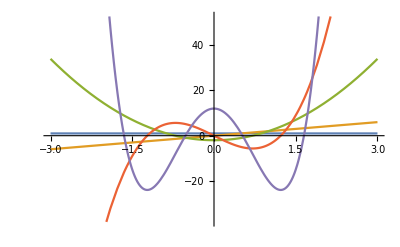

```mathematica
Plot[{HermiteH[0,x],HermiteH[1,x],HermiteH[2,x],HermiteH[3,x],HermiteH[4,x]},{x,-3,3}]
```

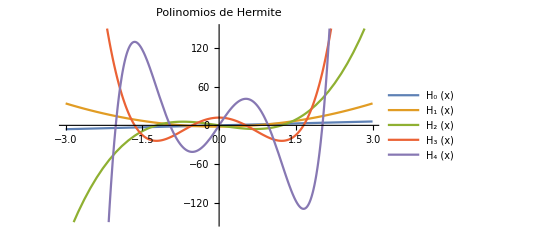

```mathematica
poliHermite[n_]:=HermiteH[n,x]

Plot[Evaluate[poliHermite/@Range[5]],{x,-3,3}, PlotLabel->Style["Polinomios de Hermite", FontSize->14, Black], PlotLegends->{"H_0 (x)","H_1 (x)","H_2 (x)","H_3 (x)", "H_4 (x)","H_5 (x)",},PlotRange->{{-3,3},{-150,150}}]
```